```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
(*DGLAP段只有ξ到3ξ*)
```

```mathematica
(*pi+result*)
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
Hdaf=Interpolation[Flatten[Hdau,1]];
Edgf=0;
Eerf=0;
Edaf=0;
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;

dHerf=Interpolation[Flatten[dHeru,1]];
dHdaf=Interpolation[Flatten[dHdau,1]];

dEerf=Interpolation[Flatten[dEeru,1]];
dEdaf=Interpolation[Flatten[dEdau,1]];
Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-D-up-xi1-pi.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
DHdaf=Interpolation[Flatten[DHdau,1]];


dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-dleta-D-pi-xi1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHerf=Interpolation[Flatten[dDHeru,1]];
dDHdaf=Interpolation[Flatten[dDHdau,1]];
dDEerf=Interpolation[Flatten[dDEeru,1]];
dDEdaf=Interpolation[Flatten[dDEdau,1]];
```

```mathematica
dgpdur=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-dleta-pi-xi1-right.wdx"];
dHdgur=Query[1,1]@dgpdur;
dHerur=Query[1,2]@dgpdur;
dHdaur=Query[1,3]@dgpdur;
dEdgur=Query[2,1]@dgpdur;
dEerur=Query[2,2]@dgpdur;
dEdaur=Query[2,3]@dgpdur;

dHerfr=Interpolation[Flatten[dHerur,1]];
dHdafr=Interpolation[Flatten[dHdaur,1]];

dEerfr=Interpolation[Flatten[dEerur,1]];
dEdafr=Interpolation[Flatten[dEdaur,1]];

dDgpdur=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-i-dleta-D-pi-xi1-right.wdx"];

dDHerur=Query[1,2]@dDgpdur;
dDHdaur=Query[1,3]@dDgpdur;

dDEerur=Query[2,2]@dDgpdur;
dDEdaur=Query[2,3]@dDgpdur;

dDHerfr=Interpolation[Flatten[dDHerur,1]];
dDHdafr=Interpolation[Flatten[dDHdaur,1]];

dDEerfr=Interpolation[Flatten[dDEerur,1]];
dDEdafr=Interpolation[Flatten[dDEdaur,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t]+dHerf[x,t]+dHdaf[x,t]+DHerf[x,t]+DHdaf[x,t]+dDHerf[x,t]+dDHdaf[x,t]+dHdafr[x,t]+dDHdafr[x,t];
Edgall[x_,t_]:=Edgf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t]+dEerf[x,t]+dEdaf[x,t]+dDEerf[x,t]+dDEdaf[x,t]+dEdafr[x,t]+dDEdafr[x,t];
```

```mathematica
Herall2[x_,t_]:=Herf[x,t]+Hdaf[x,t]+dHerf[x,t]+dHdaf[x,t]+DHerf[x,t]+DHdaf[x,t]+dDHerf[x,t]+dDHdaf[x,t];
```

```mathematica
(*tadpole图先按照bubble图的方式进行考虑，也就是把p1+p1-圈就当作一个pi+*)
```

```mathematica
(*u quark*)
```

```mathematica
(*npi+,只需要乘上系数*)
Coep1=(-I)*(1/(2*(2π)^4*fc^2))*(1/2);
(*pi+的u贡献，无需其他反转*)
p1Hdg[x_,t_]=Coep1*Hdgall[x,t];
p1Her[x_,t_]=Coep1*Herall[x,t];

p1Edg[x_,t_]=Coep1*Edgall[x,t];
p1Eer[x_,t_]=Coep1*Eerall[x,t];
(*图的总结果，就是对粒子求和*)
Hdgzall[x_,t_]=p1Hdg[x,-t];
Herallwhole[x_,t_]=p1Her[x,-t];
Edgzall[x_,t_]=p1Edg[x,-t];
Eerallwhole[x_,t_]=p1Eer[x,-t];
```

```mathematica
p1Her2[x_,t_]=Coep1*Herall2[x,t];
Herallwhole2[x_,t_]=p1Her2[x,-t];
```

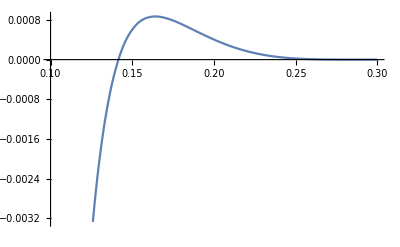

```mathematica
Plot[Hdgzall[x,1],{x,0.1,0.3}]
```

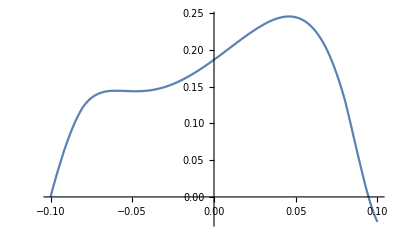

```mathematica
Plot[Herallwhole[x,1],{x,-0.1,0.1}]
```

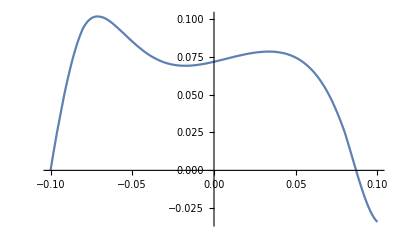

```mathematica
Plot[Herallwhole2[x,1],{x,-0.1,0.1}]
```

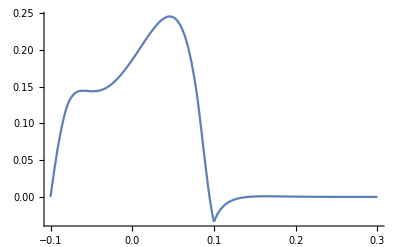

```mathematica
Show[Plot[Hdgzall[x,1],{x,0.1,0.3},PlotRange->All],Plot[Herallwhole[x,1],{x,-0.1,0.1},PlotRange->All]]
```

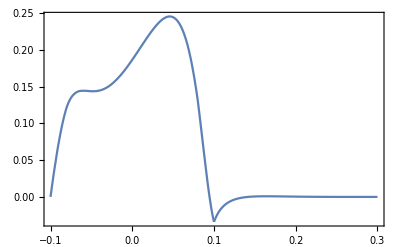
-Graphics-H_uxdiagram i

-Graphics-E_uxdiagram i

```mathematica
pHu2d=Labeled[Show[Plot[Hdgzall[x,1],{x,0.1,0.3},PlotRange->All],Plot[Herallwhole[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_u","x","diagram i"},{Left,Bottom,Top},LabelStyle->24]
pEu2d=Labeled[Show[Plot[Edgzall[x,1],{x,0.1,1},PlotRange->All],Plot[Eerallwhole[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_u","x","diagram i"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
(*pathH=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"H-f-2d.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\pic\\gpd-caogao\\717",
"E-f-2d.pdf"}];
```

```mathematica
(*Export[pathH,pHu2d]
```

```mathematica
(*Export[pathE,pEu2d]
```

```mathematica
Herall[-0.07,-1]
```

0.+7.59886 ⅈ

```mathematica
Herf[-0.07,-1]
```

0.-0.241047 ⅈ

```mathematica
Hdaf[-0.07,-1]
```

0.-4.99856 ⅈ

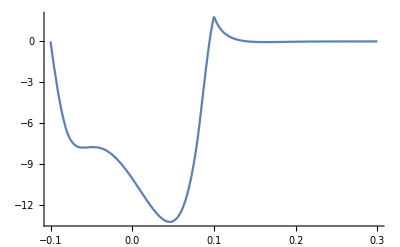

```mathematica
Show[Plot[I*Hdgall[x,-1],{x,0.1,0.3},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

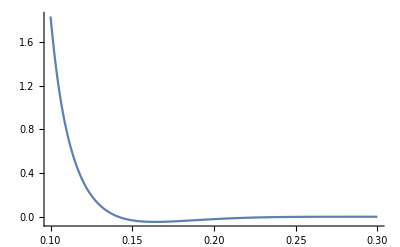

```mathematica
Plot[I*Hdgall[x,-1],{x,0.1,0.3},PlotRange->All]
```

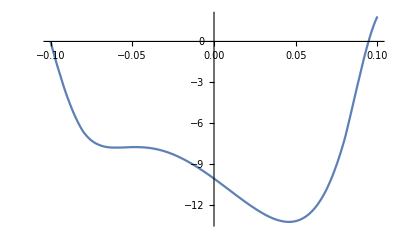

```mathematica
Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]
```

```mathematica
p1Hdg
```

p1Hdg

```mathematica
Show[Plot[I*p1Hdg[x,-1],{x,0.1,1},PlotRange->All],Plot[I*p1Her[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

-Graphics-

```mathematica
(*d quark*)
```

```mathematica
(*npi+,dbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
p1Hdgd[x_,t_]=-p1Hdg[-x,t];
p1Herd[x_,t_]=-p1Her[-x,t];

p1Edgd[x_,t_]=-p1Edg[-x,t];
p1Eerd[x_,t_]=-p1Eer[-x,t];


(*pi0,u=d，所以直接套用u的形式*)
(*图的总结果，就是对粒子求和*)
Hdgfalld[x_,t_]=p1Hdgd[x,-t];
Herallwholed[x_,t_]=p1Herd[x,-t];
Edgfalld[x_,t_]=p1Edgd[x,-t];
Eerallwholed[x_,t_]=p1Eerd[x,-t];
```

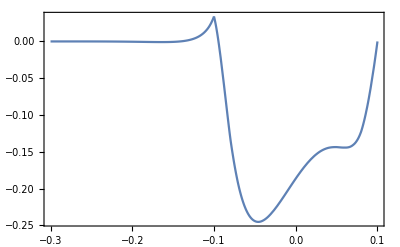
-Graphics-H_dxdiagram i

-Graphics-E_dxdiagram i

```mathematica
pHd2d=Labeled[Show[Plot[Hdgfalld[x,1],{x,-0.3,-0.1},PlotRange->All],Plot[Herallwholed[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram i"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgfalld[x,1],{x,-0.3,-0.1},PlotRange->All],Plot[Eerallwholed[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram i"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-i.wdx"}];
pathd=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"d-diagram-i.wdx"}];
outu=<|"H"-><|"DGz"->Hdgzall[x,t],"ER"->Herallwhole[x,t],"DGf"->0|>,"E"-><|"DGz"->Edgzall[x,t],"ER"->Eerallwhole[x,t],"DGf"->0|>|>;
outd=<|"H"-><|"DGz"->0,"ER"->Herallwholed[x,t],"DGf"->Hdgfalld[x,t]|>,"E"-><|"DGz"->0,"ER"->Eerallwholed[x,t],"DGf"->Edgfalld[x,t]|>|>;
Export[pathu,outu]
Export[pathd,outd]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-i.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\d-diagram-i.wdx